```mathematica
ClearAll["Global`*"]
```

```mathematica
inertia[m_, r_, a_, rL_, n_, d_]:=1/2 m (r^2 + a^2-Pi rL^2/(Pi r^2 - n Pi rL^2) n (rL^2 + d^2(n+1)(2n+1)/3))
```

```mathematica
T[a_]=Sqrt[4.0Pi^2(1/2+1a^2)/a/9.81]
```

2.00607 √((1/2+a^2)/a)

```mathematica
T[1]
```

2.45692

```mathematica
T[2]
```

3.0091

```mathematica
T[3]
```

3.56982

```mathematica
T[4]
```

4.07434

## Fehlerfortpflanzung

```mathematica
D[4 Pi^2 / mu, mu]
```

-(4 π^2)/mu^2

```mathematica
D[nu / (4*Pi^2) * m * g, nu]
```

(g m)/(4 π^2)

```mathematica
D[nu / (4*Pi^2) * m * g, g]
```

(m nu)/(4 π^2)

```mathematica
D[nu / (4*Pi^2) * m * g, m]
```

(g nu)/(4 π^2)

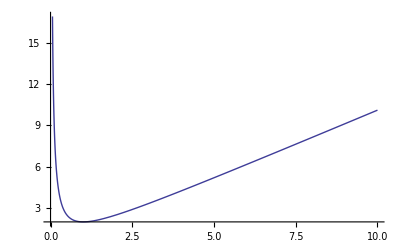

```mathematica
Plot[(1+a^2)/a, {a, 0, 10}]
```